```mathematica
clearVariables[]
setVariables[]

T1 = 5*10^-9;
T2 = 300*10^-9;
Tmax = 2*T1 + T2;

paramSets = {};
δEs = {};

Do[(
ΔEMid = 0;
ΔE = twoPointWindowFromPoints[t, 10000, T1, -2000, Tmax - T1,2000, Tmax] + δE;
ϵ0Mid = ϵ0 /. ΔE->ΔEMid;

λ = .7;
Ea =λ*116.68;
ωE = 2*π*(ϵ0 - A/4 + A*dState[[1]]^2/2) - 2*π*2.0548*10^8 /. ΔE->ΔEMid;

Ba = λ*0.015131;
ωB = 2*π*(B0*γe - A*dState[[1]]^2/2) - 2*π*1.9759*10^8 /. ΔE->ΔEMid;

UbaseLab = MatrixExp[-ⅈ*t*(HexactStatic /. t->0)];
Ubase0 = MatrixExp[-ⅈ*t*(H0static /. t->0)];
Ubase = MatrixExp[-ⅈ*t*(HcorrectedStatic /. t->0)];

Eamp[t_] := Ea*cosWindow[t - T1, T2/10, T2];
Bamp[t_] := Ba*cosWindow[t - T1, T2/10, T2];

(*Hexactδ = Hexact;
Hcorrectedδ = Hcorrected;*)

statusString="δE = " <> ToString[δE] <> "          ";
U = findEvolutionOperator2D[Hcorrected, Tmax];
(*Ufull = findEvolutionOperator[Hcorrected, Tmax];*)
UU = U /. t->Tmax;

params = gateDecompositionParameters[UU];
AppendTo[δEs, δE];
AppendTo[paramSets, params];
), {δE, -500, 500, 25}
]
```

7.24613+0.0106437 x

5.2244+0.00772403 x

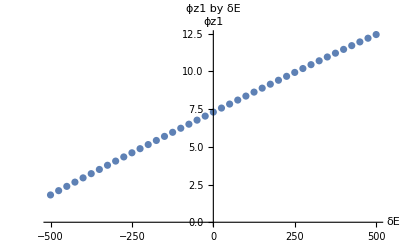

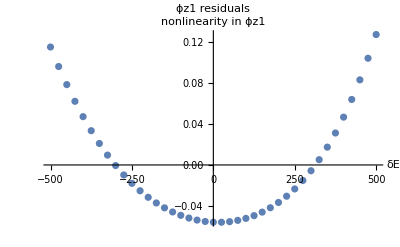

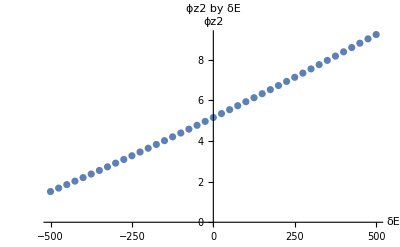

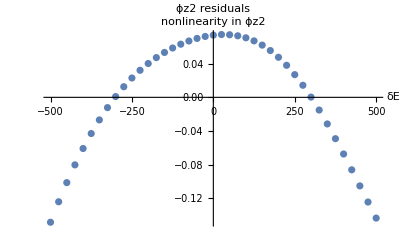

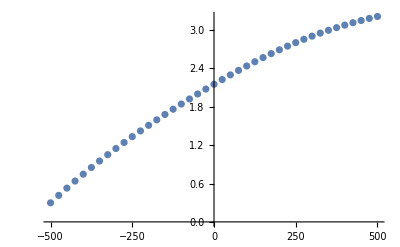

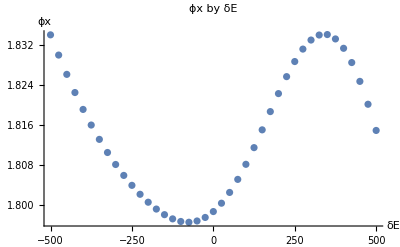

```mathematica
unravel[input_] := (
output = input;
Do[(
If[output[[i + 1]] - output[[i]] > π, output[[i + 1;;]] = output[[i + 1;;]] - 2π];
If[output[[i + 1]] - output[[i]] < -π, output[[i + 1;;]] = output[[i + 1;;]] + 2π];
),{i, Length[input] - 1}
];
output
)

fullData = Transpose[paramSets];

γs = unravel[fullData[[3]]];
βs = unravel[fullData[[2]]];
αs = unravel[fullData[[1]]];
Fit[Transpose[{δEs, γs}], {1, x}, x]
Fit[Transpose[{δEs, αs}], {1, x}, x]

γResids = (Fit[Transpose[{δEs, γs}], {1, x}, x] /. x->δEs) - γs;
αResids = (Fit[Transpose[{δEs, αs}], {1, x}, x] /. x->δEs) - αs;

ListPlot[Transpose[{δEs, γs}], PlotLabel->"ϕz1 by δE", AxesLabel->{"δE", "ϕz1"}]
ListPlot[Transpose[{δEs, γResids}], PlotLabel->"ϕz1 residuals", AxesLabel->{"δE", "nonlinearity in ϕz1"}]

ListPlot[Transpose[{δEs, αs}], PlotLabel->"ϕz2 by δE", AxesLabel->{"δE", "ϕz2"}]
ListPlot[Transpose[{δEs, αResids}], PlotLabel->"ϕz2 residuals", AxesLabel->{"δE", "nonlinearity in ϕz2"}]

ListPlot[Transpose[{δEs, γs - αs}]]

ListPlot[Transpose[{δEs, βs}], PlotLabel->"ϕx by δE", AxesLabel->{"δE", "ϕx"}]
```

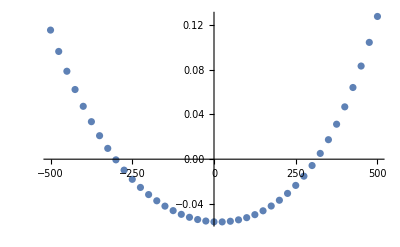

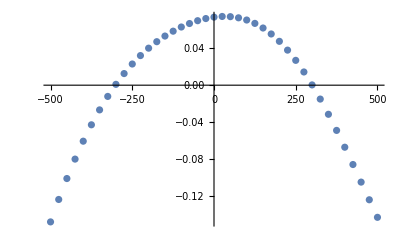

```mathematica
γResids = (Fit[Transpose[{δEs, γs}], {1, x}, x] /. x->δEs) - γs;
αResids = (Fit[Transpose[{δEs, αs}], {1, x}, x] /. x->δEs) - αs;
ListPlot[Transpose[{δEs, γResids}]]
ListPlot[Transpose[{δEs, αResids}]]
```

```mathematica
clearVariables[]
Series[δRot[1, 2], {ΔE, 0, 1}] // FullSimplify
```

(-1/2 π (A+4 B0 γn)-ωB+ωE)+(A d e π ΔE)/(2 h Vt)+O[ΔE]^2

```mathematica
Eigensystem[σZ + σX]
```

{{-√2,√2},{{1-√2,1},{1+√2,1}}}

```mathematica
(1/2)D[ArcTan[a, b], a]
```

-b/(2 (a^2+b^2))